## Definitions of Functions

```mathematica
(* function that computes ROC curve and AUC:
	The first argument is a matrix with an arbitrary number of rows (samples) and two columns. The first column is supposed to contain
	the discriminant values and the second column is supposed to contain the actual labels of the samples (+1/-1).
	The second argument K is optional (defaults to infinity); if used, the ROC curve is only considered up to the K-th negative sample (false positive).
	The third argument is optional; it is the color in which the curve is drawn (defaults to BIOINF blue).
	The fourth argument is also optional; it is the color in which the area under the ROC curve is drawn (defaults to white). *)

ROC[mat_,K_:Infinity,curvecolor_:RGBColor[0.204,0.325,0.631],areacolor_:White]:=Module[{pos=0,neg=0,i,m,plotlist,p=0,n=0,prev,auc=0},
	m=Length[mat];
	list=mat[[Ordering[mat[[All,1]]]]][[All,2]];
	For[j=m,j>=1 && neg<K,j--,
		If[list[[j]]>0,pos++,neg++]];
	plotlist={{0,0}};
	If[pos>0,For[i=m,i>=j && n<K,i--,
		If[list[[i]]>0,p++,n++;auc+=(p/(pos*neg))];
		plotlist=Append[plotlist,{n/neg,p/pos}]],
		plotlist=Append[plotlist,{1,0}]];
	g1=Graphics[{Thickness[0.01],curvecolor,Line[plotlist]}];
	g2=Graphics[{Thickness[0.01],areacolor,Polygon[Append[plotlist,{1,0}]]}];
	If[K==Infinity,Print["AUC: ",N[auc]],Print["AUC",K,": ",N[auc]]];
	Show[g2,g1,Frame->True,FrameLabel->{FPR,TPR},AspectRatio->1,PlotRange->{{-0.02,1.02},{-0.02,1.02}},ImageSize->{400,Automatic}]];

(* function that takes a list of samples as first argument and computes their discriminant values according to the
	discriminant function supplied as second argument *)
Classify[testset_,classifier_]:=Map[{classifier[#],#[[-1]]}&,testset];
```

## Example 1: Assessing how well thresholding of the components would solve a classification problem

#### Compute ROC and ROC5 for DataSet6 using the first component as discriminant function (which corresponds to thresholding this component)

AUC: 0.42042

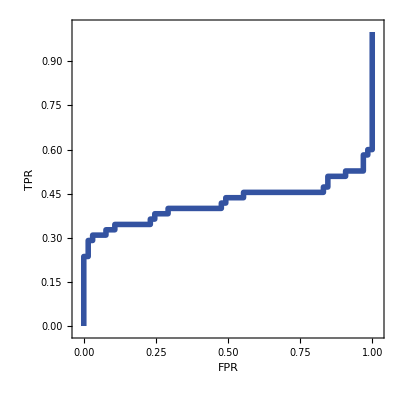

AUC50: 0.8672

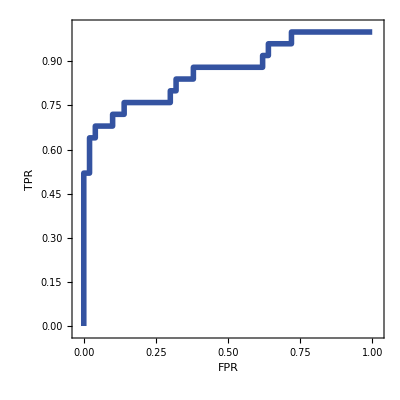

```mathematica
ROC[Classify[DataSet6,#[[1]] &]]
ROC[Classify[DataSet6,#[[1]] &],50]
```

#### Compute ROC and ROC5 for DataSet6 using the second component as discriminant function (which corresponds to thresholding this component)

AUC: 0.993566

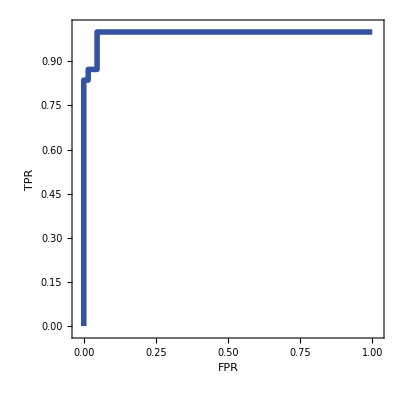

AUC50: 0.991636

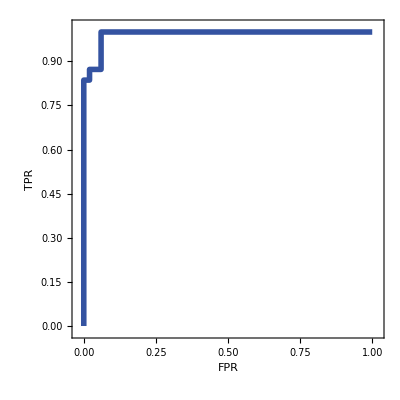

```mathematica
ROC[Classify[DataSet6,#[[2]] &]]
ROC[Classify[DataSet6,#[[2]] &],50]
```

## Example 2: ROC applied to KNN

#### Compute ROC and ROC50 for the 1-nearest neighbor classifier applied to DataSet2, where the first 80 samples are used for "training" and the remaining 40 samples are the test samples

AUC: 0.786667

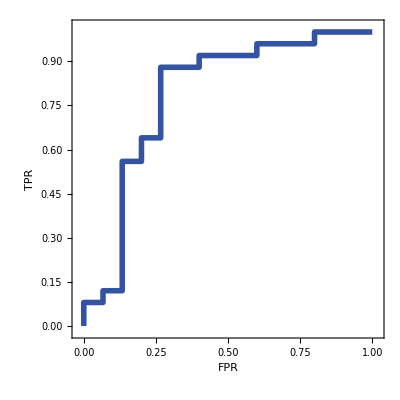

AUC50: 0.786667

-Graphics-

```mathematica
ROC[Classify[Take[DataSet2,-40],KNN[#,Take[DataSet2,80],1] &]]
ROC[Classify[Take[DataSet2,-40],KNN[#,Take[DataSet2,80],1] &],50]
```

#### Compute ROC and ROC50 for the 5-nearest neighbor classifier applied to DataSet2, where the first 80 samples are used for "training" and the remaining 40 samples are the test samples

AUC: 0.96

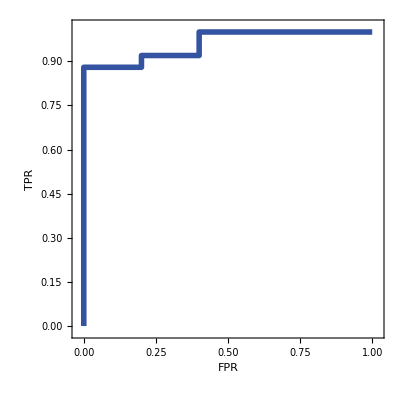

AUC50: 0.96

-Graphics-

```mathematica
ROC[Classify[Take[DataSet2,-40],KNN[#,Take[DataSet2,80],5] &]]
ROC[Classify[Take[DataSet2,-40],KNN[#,Take[DataSet2,80],5] &],50]
```

## Example 3: an artificial data set

#### Create a list of 2D vectors with ascending numbers in the first component and random -1/+1 labels in the second component (with increasing i, the probability of +1 increases linearly)

AUC: 0.863368

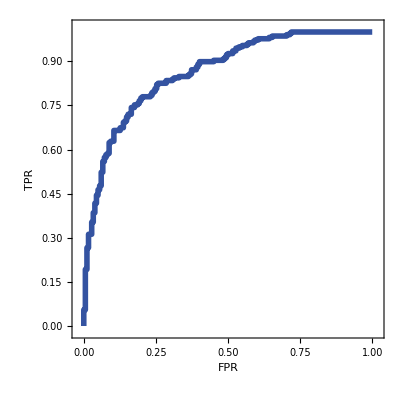

AUC50: 0.765556

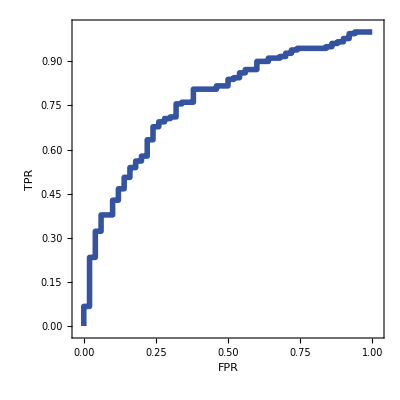

```mathematica
prlist=Table[{i,If[RandomReal[]>i/400,-1,1]},{i,1,400}];
ROC[prlist]
ROC[prlist,50]
```

## Example 4: the two ROC-Ex data sets (protein classification)

```mathematica
Compute ROC and ROC50 for the ROC-Ex1 data set
```

AUC: 0.695933

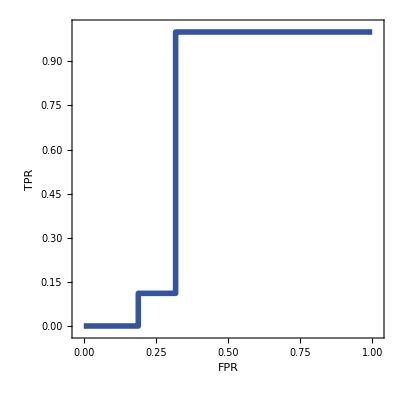

AUC50: 0.

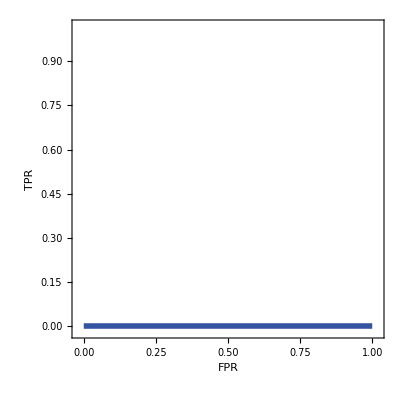

```mathematica
ROC[RocEx1]
ROC[RocEx1,50]
```

```mathematica
Compute ROC and ROC50 for the ROC-Ex2 data set
```

AUC: 0.912075

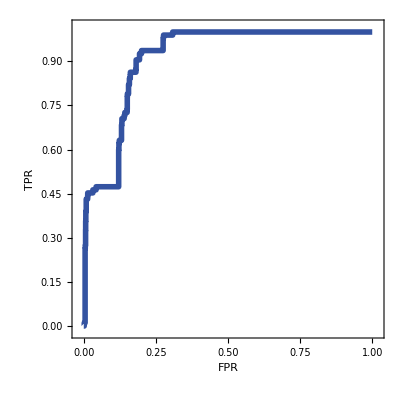

AUC50: 0.585238

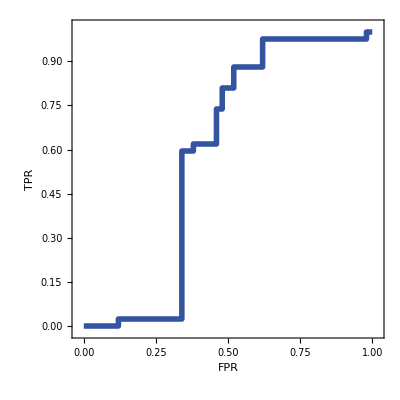

```mathematica
ROC[RocEx2]
ROC[RocEx2,50]
```